Alec Ramos

```mathematica
1
```

```mathematica
f[x_]:= Tan[x]
```

```mathematica
g[x_]:= Sec[x]
```

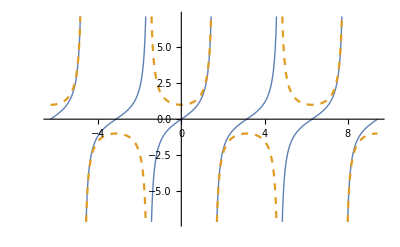

```mathematica
Show[Plot[{f[x], g[x]}, {x, -2π, 3π}, PlotStyle-> {Thick, Dashed}] ]
```

```mathematica
2
```

```mathematica
f[x_]:= Cos[x]
```

```mathematica
g[x_]:= Sin[x]
```

```mathematica
Solve[{f[x]==g[x], 0≤x≤2π}]
```

{{x→-2 ArcTan[1-√2]},{x→2 π-2 ArcTan[1+√2]}}

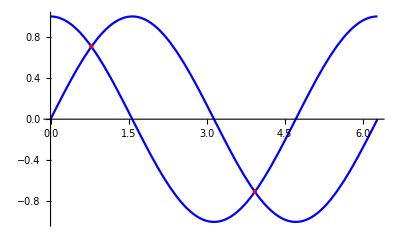

```mathematica
Show[Plot[{f[x], g[x]}, {x, 0, 2π}, PlotStyle->{Blue}],
Graphics[{Red, PointSize[Large],
Point[{
{-2 ArcTan[1-√2], f[-2 ArcTan[1-√2]]}, {2 π-2 ArcTan[1+√2], f[2 π-2 ArcTan[1+√2]]}
}]
}]
]
```

```mathematica
3
```

```mathematica
f[x]:= Tan[x]
```

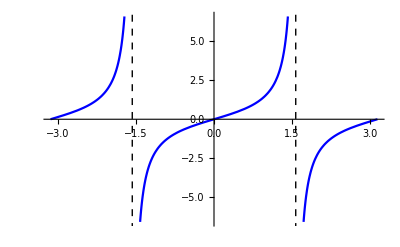

```mathematica
Show[Plot[f[x], {x, -π, π}, PlotStyle-> {Blue}],
Graphics[{
{Black, Dashed,Line[{
{{-π/2,-8},{-π/2,8}},{{π/2,-8},{π/2,8}}
}]}
}]
]
```